### initial analysis

```mathematica
ClearAll
```

ClearAll

```mathematica
Integrate[1/(s-Cos[θ]),{θ,0,2Pi}]
```

ConditionalExpression[Piecewise[{{-(2 π)/(√(-1+s^2)), Abs[s-√(-1+s^2)]≥1&&Abs[s+√(-1+s^2)]<1}, {(2 π)/(√(-1+s^2)), Abs[s-√(-1+s^2)]<1&&Abs[s+√(-1+s^2)]≥1}, {0, True}}], ]

```mathematica
Integrate[1/(.1-Cos[θ]),{θ,0,2Pi}]
```

-0.251689

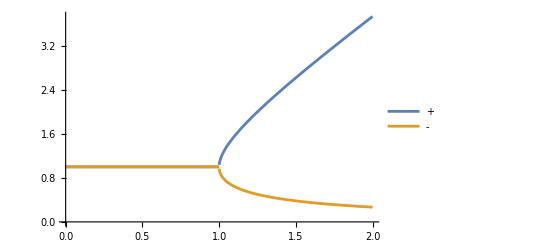

```mathematica
Plot[{Abs[x+Sqrt[x^2-1]],Abs[x-Sqrt[x^2-1]]},{x,0,2},PlotLegends->{"+","-"}]
```

```mathematica
Abs[zm[.1,.2]]
```

0.819026

```mathematica
zp[x_,y_]=(x+I y)+Sqrt[(x+I y)^2-1];
zm[x_,y_]=(x+I y)-Sqrt[(x+I y)^2-1];
Abs[zp[.1,.2]]
Abs[zp[.1,.2]]
```

1.22096

1.22096

```mathematica
Plot3D[{1,Abs[zm[x,y]]},{x,-2,2},{y,-2,2},ImageSize->Small]
```

-Graphics3D-

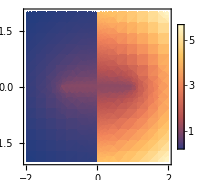

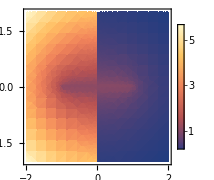

```mathematica
DensityPlot[Abs[zp[x,y]],{x,-2,2},{y,-2,2},PlotLegends->Automatic,ImageSize->Small]
DensityPlot[Abs[zm[x,y]],{x,-2,2},{y,-2,2},PlotLegends->Automatic,ImageSize->Small]
```

#### plot 1

```mathematica
FR[a_]:=1/Pi NIntegrate[1/(2Pi)ArcTan[a/(2 Sin[θ/2]^3)]Sin[θ/2],{θ,0,2Pi}]
FI[a_]:=1/(2Pi)NIntegrate[1/(2Pi)Log[1+a^2/Sin[θ/2]^6]Sin[θ/2],{θ,0,2Pi}];
```

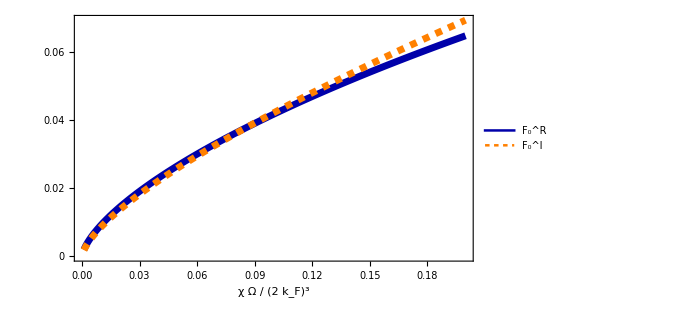

```mathematica
freq=Table[i*.001,{i,1,200}];
dataFR=Table[{i,FR[i]},{i,.001,200*.001,.001}];
dataFI=Table[{i,FI[i]},{i,.001,200*.001,.001}];
pl=ListPlot[{dataFR, dataFI},PlotRange->All, Joined->True,Axes->None,Filling->Blank,Frame-> True,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,Bold},LabelStyle->Directive[Black,24],FrameTicks->{{{0,0.02,0.04,.06,.08},None},{Automatic,None}},FrameTicksStyle->Directive[Darker[Gray],18],FrameLabel->{Style["χ Ω / (2 k_F)^3",FontFamily->"LM Roman 10",Black, Bold, 24],None},PlotStyle->style,
PlotLegends->Placed[LineLegend[{"F_0^R","F_0^I"},LabelStyle->{FontFamily->"LM Roman 10",20},LegendLayout->"Row"],{Scaled[{0.5,1}],{0,5.05}}],ImageSize->500]
SetDirectory[NotebookDirectory[]];
Export["F0.pdf",Rasterize[pl],ImageResolution->100];
```

#### other stuff

```mathematica
FR[.1]
```

0.0833563

```mathematica
Plot[FR[a],{a,0,1}]
```

$Aborted

```mathematica
(0.4)^(3/2)
```

0.252982

```mathematica
Series[FR[a],{a,0,2},Assumptions->a>0]//N
```

Series::ztest1: Unable to decide whether numeric quantity 4-(2 Gamma[1/3] Gamma[2/3])/(√3 Gamma[5/6] Gamma[7/6]) is equal to zero. Assuming it is.

0.401045 (a+0.)^(2/3)-0.0631607 (a+0.)^(4/3)-0.00994718 (a+0.)^2+O[a+0.]^(7/3)

```mathematica
Series[FI[a],{a,0,2},Assumptions->a>0]//N
```

0.367553 (a+0.)^(2/3)+0.0918881 (a+0.)^(4/3)-0.0253303 (-0.829442+1. Log[0.+a]) (a+0.)^2+O[a+0.]^(7/3)

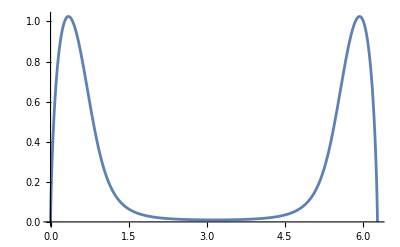

```mathematica
Plot[Log[1+(.1)^2/Sin[θ/2]^6]Sin[θ/2],{θ,0,2Pi}]
```

```mathematica
Abs[zp[0.0,-0.1]]
```

0.904988

```mathematica
Manipulate[Plot[{1,Abs[zm[x,y]]},{y,-2,2}],{x,0,2}]
```

```mathematica
SolQBE[q_,Fr_,Fi_]:=Module[{a1,a2,a3,a4},a1=Solve[si^4+si^2(q^2+Fr^2-Fi^2)-Fr^2*Fi^2==0,si,Assumptions->{Fr>0,Fi>0,q>0,si>=0}];
a2=Table[a1[[i,1,2]],{i,1,Dimensions[a1][[1]]}][[1]];
a3=Fr*Fi/a2;
a4=a3+I*a2;
a4]
```

### plot 2

### my try

```mathematica
Sov[Ω0_,q_]:=Module[{a1,a2,a3},a1=Solve[ x^2(1+2(Ω0/x)^(1/3))(1+2(Ω0/x)^(1/3)+2(Ω0/x)^(2/3))==(1+(Ω0/x)^(1/3))^2 q^2,x,Assumptions->{x>0,x+Ω0^(1/3)x^(2/3)>=0}][[1,1,2]];
a2=Ω0^(2/3)a1^(4/3)/(Ω0^(1/3)a1^(2/3)+a1)-Ω0^(1/3)a1^(2/3);
a1+I*a2]
Sov0[Ω0_,q_]:=Module[{a1,a2,a3},a1=Solve[ x^2(1+2(Ω0/x)^(1/3))==q^2,x,Assumptions->{x>0,x+Ω0^(1/3)x^(2/3)>=0}][[1,1,2]];
a1]
```

```mathematica
x=Ω0;
Solve[ x^2(1+2(Ω0/x)^(1/3))(1+2(Ω0/x)^(1/3)+2(Ω0/x)^(2/3))==(1+(Ω0/x)^(1/3))^2 q^2,q]
Clear[x];
```

{{q→-(√15 Ω0)/2},{q→(√15 Ω0)/2}}

{a→1.13981,b→1.19657}

{a→0.336705,b→1.0541}

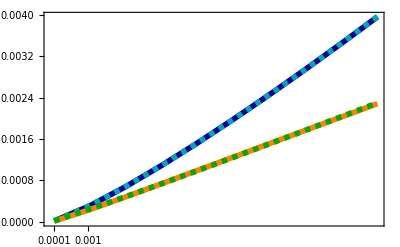

```mathematica
Om0=0.01;
dat1=Table[{q,Sov[Om0,q]},{q,0.0001,(√15 Om0)/4,(√15 Om0)/2/20}]//Quiet;
list=dat1;
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],-Im[list[[i,2]]]},{i,1,len}];
th=0.01;
style={Directive[Darker[Blue],Thickness[0.01]],Directive[Orange,Thickness[0.01]],Directive[Darker[Cyan],Thickness[0.01],Dashing[0.01]],Directive[Darker[Green],Thickness[0.01],Dashing[0.01]]};

FindFit[Drop[dat1,-1],a  q^b,{a,b},q]
datfitr=Table[{q,a  q^b/. %},{q,0.0001,(√15 Om0)/4,(√15 Om0)/2/20}];
FindFit[Drop[dat2,-1],a  q^b,{a,b},q]
datfiti=Table[{q,a  q^b/. %},{q,0.0001,(√15 Om0)/4,(√15 Om0)/2/20}];
ListPlot[{dat1, dat2,datfitr,datfiti}, Joined->True,Axes->None,Frame-> True,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],18],FrameTicks->{{Automatic,None},{{.0001,.001, .01,.1},None}},PlotStyle->style]
```

```mathematica
Rationalize[1.2]
```

6/5

{a→0.874281,b→1.12433}

{a→0.174018,b→0.881627}

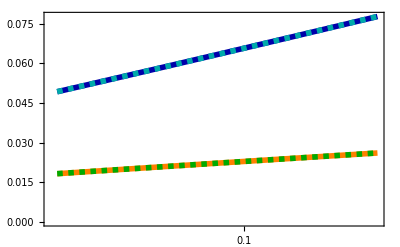

```mathematica
Om0=0.01;
dat1=Table[{q,Sov[Om0,q]},{q,(√15 Om0)/2 4,(√15 Om0)/2 6,√15 Om0/20}]//Quiet;
list=dat1;
len=Length[list];
dat1=Table[{list[[i,1]],Re[list[[i,2]]]},{i,1,len}];
dat2=Table[{list[[i,1]],-Im[list[[i,2]]]},{i,1,len}];
th=0.01;
style={Directive[Darker[Blue],Thickness[0.01]],Directive[Orange,Thickness[0.01]],Directive[Darker[Cyan],Thickness[0.01],Dashing[0.01]],Directive[Darker[Green],Thickness[0.01],Dashing[0.01]]};

FindFit[Drop[dat1,-1],a  q^b,{a,b},q]
datfitr=Table[{q,a  q^b/. %},{q,(√15 Om0)/2 4,(√15 Om0)/2 6,√15 Om0/20}];
FindFit[Drop[dat2,-1],a  q^b,{a,b},q]
datfiti=Table[{q,a  q^b/. %},{q,(√15 Om0)/2 4,(√15 Om0)/2 6,√15 Om0/20}];
ListPlot[{dat1, dat2,datfitr,datfiti}, Joined->True,Axes->None,Frame-> True,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,Bold},FrameTicksStyle->Directive[Darker[Gray],18],FrameTicks->{{Automatic,None},{{.0001,.001, .01,.1},None}},PlotStyle->style]
```

```mathematica
Rationalize[1.1]
Rationalize[0.88]
```

11/10

22/25

### other stuff

```mathematica
data0=Table[Sov0[.01,i*.001],{i,1,200}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{0.000379244,0.000848899,0.00135628,0.00188857,0.00243951,0.00300533,0.00358351,0.00417225,0.00477021,0.00537633,0.00598976,0.00660982,0.00723592,0.00786758,0.00850439,0.00914598,0.00979204,0.0104423,0.0110965,0.0117544,0.0124158,0.0130805,0.0137485,0.0144194,0.0150933,0.0157699,0.0164491,0.017131,0.0178152,0.0185018,0.0191907,0.0198818,0.0205749,0.0212701,0.0219673,0.0226664,0.0233674,0.0240702,0.0247747,0.0254809,0.0261888,0.0268982,0.0276093,0.0283218,0.0290359,0.0297513,0.0304683,0.0311865,0.0319062,0.0326271,0.0333494,0.0340729,0.0347976,0.0355235,0.0362506,0.0369789,0.0377083,0.0384388,0.0391704,0.0399031,0.0406368,0.0413716,0.0421074,0.0428441,0.0435818,0.0443205,0.0450602,0.0458007,0.0465422,0.0472846,0.0480278,0.0487719,0.0495169,0.0502627,0.0510093,0.0517567,0.052505,0.053254,0.0540038,0.0547544,0.0555057,0.0562578,0.0570106,0.0577642,0.0585184,0.0592734,0.0600291,0.0607854,0.0615424,0.0623001,0.0630585,0.0638175,0.0645771,0.0653374,0.0660983,0.0668599,0.067622,0.0683848,0.0691481,0.0699121,0.0706766,0.0714417,0.0722074,0.0729736,0.0737404,0.0745078,0.0752757,0.0760441,0.0768131,0.0775826,0.0783526,0.0791232,0.0798943,0.0806658,0.0814379,0.0822105,0.0829835,0.0837571,0.0845311,0.0853057,0.0860806,0.0868561,0.087632,0.0884084,0.0891852,0.0899625,0.0907403,0.0915184,0.0922971,0.0930761,0.0938556,0.0946355,0.0954159,0.0961966,0.0969778,0.0977594,0.0985414,0.0993238,0.100107,0.10089,0.101673,0.102457,0.103242,0.104027,0.104812,0.105597,0.106383,0.107169,0.107956,0.108743,0.10953,0.110318,0.111106,0.111895,0.112684,0.113473,0.114262,0.115052,0.115842,0.116633,0.117424,0.118215,0.119006,0.119798,0.120591,0.121383,0.122176,0.122969,0.123763,0.124556,0.125351,0.126145,0.12694,0.127735,0.12853,0.129326,0.130122,0.130918,0.131715,0.132512,0.133309,0.134106,0.134904,0.135702,0.1365,0.137299,0.138098,0.138897,0.139697,0.140496,0.141296,0.142097,0.142897,0.143698,0.144499,0.1453,0.146102,0.146904,0.147706,0.148509}

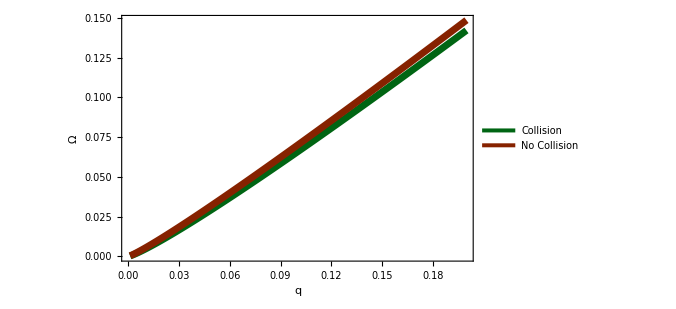

```mathematica
p2=ListPlot[{Transpose@{Momentum,Re[data]},Transpose@{Momentum,Re[data0]}},Joined->True, Frame->True,Axes->None,BaseStyle->{FontFamily->"LM Roman 10",FontSize->20,Bold},LabelStyle->Directive[Black,26],FrameStyle->Thick,FrameTicksStyle->Directive[Darker[Gray],24],FrameLabel->  {"q","Ω"},PlotStyle->{{Darker[Green],Thickness[th]},{Darker[Red],Thickness[th]},{Darker[Black],Thickness[th]},{Darker[Blue],Thickness[th]}},ImageSize->500,PlotLegends->Placed[ LineLegend[{ "Collision","No Collision","δ=∞"},LegendMarkerSize->25], Right]]
```

```mathematica
Export["freq vs q.pdf",p1]
```

freq vs q.pdf

```mathematica
Export["dispersion.pdf",p2]
```

dispersion.pdf

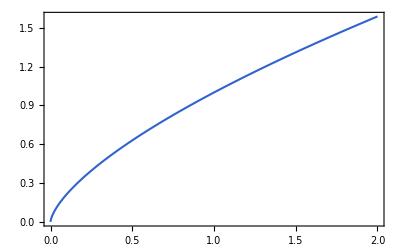

```mathematica
Plot[x^(2/3),{x,0,2}]
```

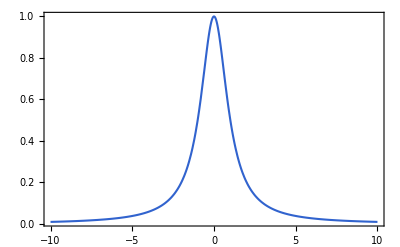

```mathematica
Plot[1/(1+x^2),{x,-10,10},PlotRange->All]
```

```mathematica
(.4)^3
```

0.064

```mathematica
Series[1/(1+x^(1/3)),{x,0,2},PlotLegends]
```

1-x^(1/3)+x^(2/3)-x+x^(4/3)-x^(5/3)+x^2+O[x]^(7/3)

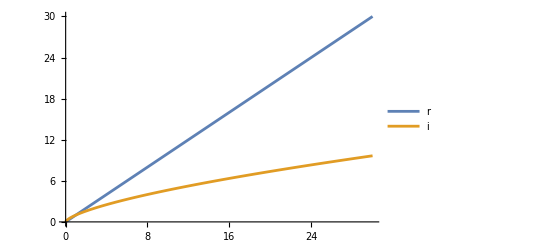

```mathematica
Plot[{x,x^(2/3)},{x,0,30},PlotLegends->{"r","i"}]
```

```mathematica
SolQBE[.4,.2,0.1]
```

0.438272+0.0456338 ⅈ

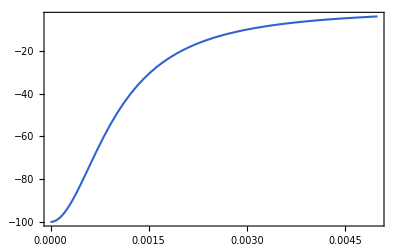

```mathematica
Plot[(-(.1)^4)/((.1)^6+x^2),{x,0,.005},PlotRange->All]
```

```mathematica
Integrate[x/(q^6+χ^2 x^2),{x,0,q},Assumptions->{q>0,χ>0}]
```

Log[1+χ^2/q^4]/(2 χ^2)

```mathematica
B[ω_,q_,χ_]:=2 χ ω q/(q^6+χ^2 ω^2)
```

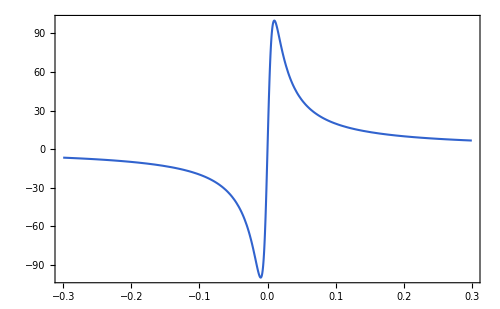

```mathematica
Plot[B[ω,.1,.1],{ω,-.3,.3},PlotRange->All,ImageSize->500]
```

```mathematica
DR[ω_,q_,χ_]:=1/((ω+I*.000001)^2-q^2+I χ ω/q)
DRFull[ω_,q_,χ_]:=1/((ω+I*.000001)^2-q^2+I χ ω/Sqrt[q^2-(ω+I*.00001)^2])
DR0[ω_,q_,χ_]:=1/(-q^2+I χ ω/q)
```

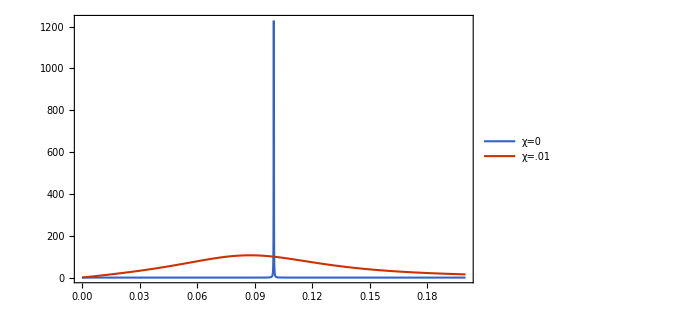

```mathematica
Plot[{ -Im[DR[ω,.1,0]],-Im[DR[ω,.1,.010]]},{ω,0,.2}, ImageSize->500,PlotRange->All,PlotLegends->{"χ=0","χ=.01"}]
```

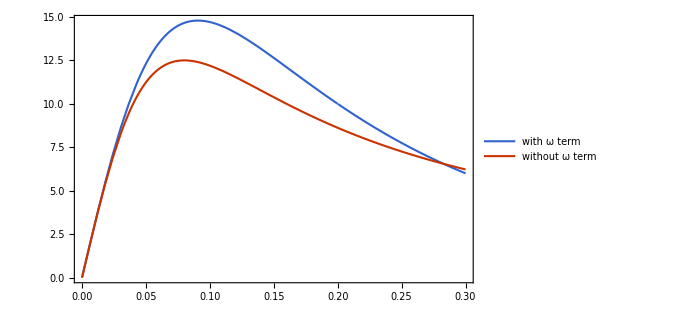

```mathematica
Plot[{ -Im[DR[ω,.2,.1]],-Im[DR0[ω,.2,.1]]},{ω,0,.3}, ImageSize->500,PlotRange->All,PlotLegends->{"with ω term","without ω term"}]
```

```mathematica
Re[DR0[ω,.1,.01]]//FullSimplify
```

Re[1/(-0.001+(0.+0.1 ⅈ) ω)]

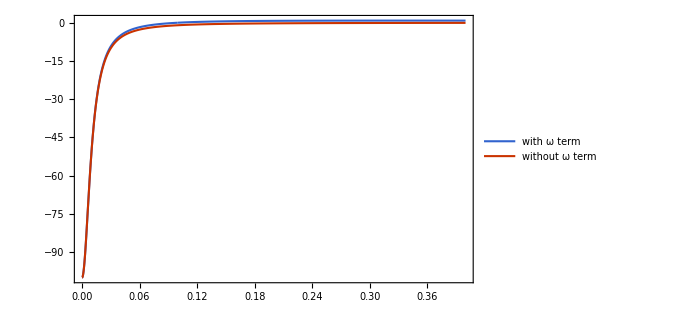

```mathematica
Plot[{ Re[DR[ω,.1,.1]],Re[DR0[ω,.1,.1]]},{ω,0,.4}, ImageSize->500,PlotRange->All,PlotLegends->{"with ω term","without ω term"}]
```

```mathematica
x^(2/3)/x
```

1/x^(1/3)

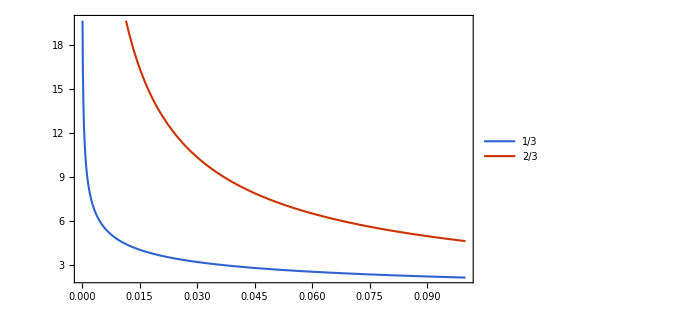

```mathematica
Plot[{1/x^(1/3),1/x^(2/3)},{x,0,.1},ImageSize->500,PlotLegends->{"1/3","2/3"}]
```

```mathematica
fermi[ω_,T_]:=1/(Exp[ω/T]+1)
correction[ωp_,ω_,T_]:=fermi[ωp+ω,T]+fermi[ωp-ω,T]-2 fermi[ωp,T]
correctionint[ω_,T_]:=NIntegrate[fermi[ωp+ω,T]+fermi[ωp-ω,T]-2 fermi[ωp,T],{ωp,-∞,∞}]
```

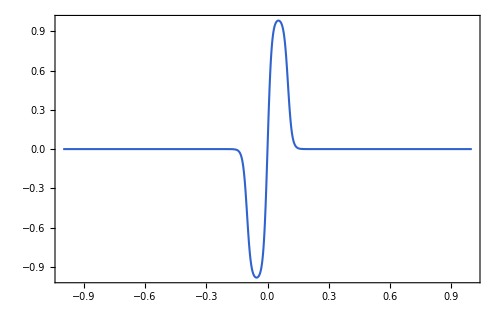

```mathematica
Plot[correction[ωp,.1,.01],{ωp,-1,1},ImageSize->500,PlotRange->All]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ωp near {ωp} = {-25.0818}. NIntegrate obtained -6.9862×10^-17 and 1.37024×10^-15 for the integral and error estimates.

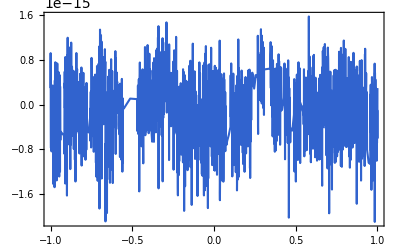

```mathematica
Plot[correctionint[ω,1],{ω,-1,1}]
```

```mathematica
{q,q^(0.96)}/.q->0.0001
```

{0.0001,0.000144544}

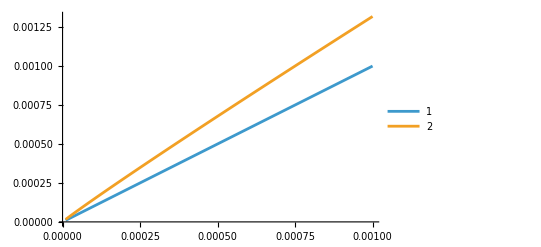

```mathematica
Plot[{q,q^(0.96)},{q,0.00001,0.001},PlotLegends->Automatic]
```